# Style

```mathematica
dir=NotebookDirectory[];
(*(*set dir as the image directory*)
dir=ParentDirectory[dir]<>"/img3/"*)
```

```mathematica
(*Styling of the text*)
st[text_]:=Style[text,Directive[15,FontFamily->"Linux Libertine Display O"]];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor[{200.,35.,0.}/255];
```

# No projections

```mathematica
(* approximant size *)
n=5;
```

```mathematica
(* the slope of the doubled unit cell *)
α=1/GoldenRatio;
θ=ArcTan[α];
Δ=2;
z2=Flatten[Table[{x,y},{x,-Δ,Fibonacci[n+1]-1+Δ},{y,-Δ,Fibonacci[n]-1+Δ}],1];
square[{x_,y_}]:=Rectangle[{x,y},{x+1,y+1}];
```

```mathematica
(* projection axis *)
cut=Line[{{0.,0.},1.18Fibonacci[n+1]{Cos[θ ],Sin[θ]}}];
(* upper limit of the selection region *)
window=Line[{{-1,1},{-1,1}+.948Fibonacci[n+1]{Cos[θ ],Sin[θ]}}];
```

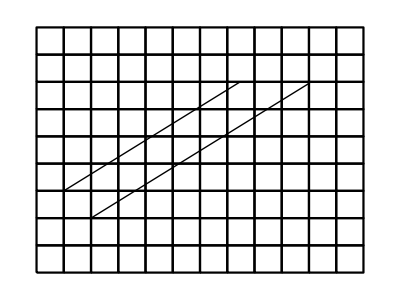

```mathematica
Graphics[{cut,window,{EdgeForm[{Thickness[0.004],Opacity[1.]}],Opacity[0],square/@z2}}]
```

```mathematica
(* enumerate the coordinates of the selected points *)
r[i_]:={Floor[i/(1+α)],i-Floor[i/(1+α)]};
```

```mathematica
z2p=Flatten[Table[{x,y},{x,-1,Fibonacci[n+1]-1},{y,0,Fibonacci[n]-1}],1];
lattice={EdgeForm[{Thickness[0.004],Opacity[0.4]}],Opacity[0],square/@z2p};
```

```mathematica
Col[{p1_,p2_ }]:=If[p2-p1=={1,0},BostonBlue,comp];
ColLine[pts_]:={Col[pts],Line[pts]};
```

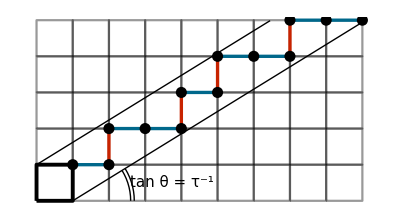

/home/nicolas/git/talks/2017 PhD Defense/img/2_part1/CP_fibo_cut.pdf

```mathematica
selPts=r/@Range[1,Fibonacci[n+2]];
fiboPts={PointSize[0.02],Point[selPts]};
staircase=ColLine/@Partition[selPts,2,1];
thicksquare={EdgeForm[Directive[Opacity[1],Thickness[0.007]]],Opacity[0],square[{-1,0}]};
(* projection angle *)
ang={Text[st@"tan θ = τ^-1",{2.75,0.5}],Circle[{0,0},#,{0,.99ArcTan[Fibonacci[n]/Fibonacci[n+1]]}]&/@{1.6,1.7}};
Graphics[{lattice,cut,window,{Thickness[0.006],staircase,fiboPts},thicksquare,ang}]
Export[dir<>"CP_fibo_cut.pdf",%]
```

```mathematica
selPts
```

{{0,1},{1,1},{1,2},{2,2},{3,2},{3,3},{4,3},{4,4},{5,4},{6,4},{6,5},{7,5},{8,5}}

```mathematica
DrawToPt[m_]:=Block[{selPts=r/@Range[1,m],fiboPts,staircase},
fiboPts={PointSize[0.02],Point[selPts]};
staircase=ColLine/@Partition[selPts,2,1];
Graphics[{lattice,{Thickness[0.008],staircase,fiboPts}}]
]
```

```mathematica
For[m=1,m≤Fibonacci[n+2],m++,
g=DrawToPt[m];
Export[dir<>"CP_fibo_"<>ToString[m]<>".pdf",g]
]
```

```mathematica
(* draw a double line for strong bonds, a single line for weak bonds *) 
(* draw a double line *)
DoubleLine[coords_,spacing_]:=Block[{Δv=coords[[2]]-coords[[1]],norm},
Δv=Δv/Norm[Δv];
(* vector normal to the direction of the line *)
norm={-Δv[[2]],Δv[[1]]};
Line[Map[Function[y,coords+y{norm,norm}],{-spacing/2,spacing/2}]]
]
spac=0.1;
cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Thickness[0.005],If[(rf-ri)[[1]]==1,Line[{proj[ri],proj[rf]}],DoubleLine[{proj[ri],proj[rf]},spac]]}];
```

```mathematica
(* project selected points into the parallel space *)
projPts=proj/@selPts;
(* lines from pts to parallel proj *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
(* projection angle *)
ang={Text[st@"tan θ = τ^-1",{2.75,0.5}],Circle[{0,0},#,{0,.9ArcTan[Fibonacci[n]/Fibonacci[n+1]]}]&/@{1.6,1.7}};
```

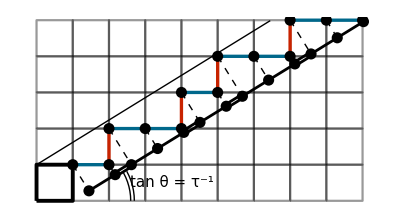

```mathematica
Graphics[{lattice,window,{Thickness[0.006],staircase,fiboPts},thicksquare,ang,{Dashed,projLines},{{PointSize[0.02],Point[projPts]},cutLine/@Range[1,Fibonacci[n+2]-1]}}]
Export[dir<>"full_cp.pdf",%];
```

# B3

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
(* B3 substitution *)
B3Sub[l_,C0_String]:=Sub[{"A"->"ABBB","B"->"A"},C0,l];
(* B3 substitution, composed 3 times *)
B3Sub3[l_,C0_String]:=Sub[{"A"->"ABBBAAAABBBABBBABBB","B"->"ABBBAAA"},C0,l];
(* return the 2D positions of the points *)
rB3[word_String]:=Accumulate[StringPartition[word,1]/.{"A"->{1,0},"B"->{0,1}}];
```

```mathematica
44-17
```

27

```mathematica
b3String=B3Sub[6,"B"];
b3String=StringTake[%,27];
selPts=rB3[b3String];
selPts=(#-{1,-1})&/@selPts;
```

```mathematica
{xM,yM}=Last[selPts];
z2p=Flatten[Table[{x,y},{x,-1,xM-1},{y,0,yM-1}],1];
lattice={EdgeForm[{Thickness[0.0001],Opacity[0.2]}],Opacity[0],square/@z2p};
```

```mathematica
α=(√13-1)/2;
θ=ArcTan[α];
(* projection axis *)
cut=Line[{{0.,1.},{0,1}+18.{Cos[θ ],Sin[θ]}}];
```

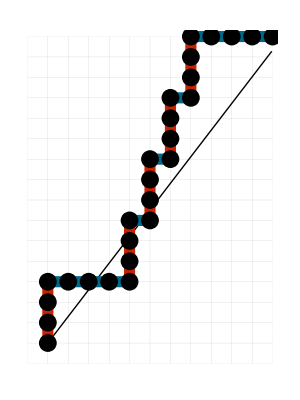

/home/nicolas/git/talks/2017 PhD Defense/img/2_part1/CP_b3_cut.pdf

```mathematica
fiboPts={PointSize[0.032],Point[selPts]};
staircase=ColLine/@Partition[selPts,2,1];
Graphics[{lattice,{Thick,cut},{Thickness[0.02],staircase,fiboPts}}]
Export[dir<>"CP_b3_cut.pdf",%]
```

# Inclined slope

```mathematica
(* approximant size *)
n=5;
```

```mathematica
(* Z^2 lattice *)
θ=-ArcTan[Fibonacci[n]/Fibonacci[n+1]];
θ=ArcTan[1/GoldenRatio];
Δ=2;
z2=Flatten[Table[{x,y},{x,-Δ,Fibonacci[n+1]-1+Δ},{y,-Δ,Fibonacci[n]-1+Δ}],1];
square[{x_,y_}]:=Rectangle[{x,y},{x+1,y+1}];
```

```mathematica
(* projection axis *)
cut=Line[{{0.,0.},1.18Fibonacci[n+1]{Cos[θ ],Sin[θ]}}];
(* upper limit of the selection region *)
window=Line[{{-1,1},{-1,1}+.948Fibonacci[n+1]{Cos[θ ],Sin[θ]}}];
```

```mathematica
Graphics[{cut,window,{EdgeForm[{Thickness[0.004],Opacity[1.]}],Opacity[0],square/@z2}}]
```

-Graphics-

```mathematica
(* enumerate the coordinates of the selected points *)
r[i_]:={Floor[i Fibonacci[n+1]/Fibonacci[n+2]],Ceiling[i Fibonacci[n]/Fibonacci[n+2]]};
```

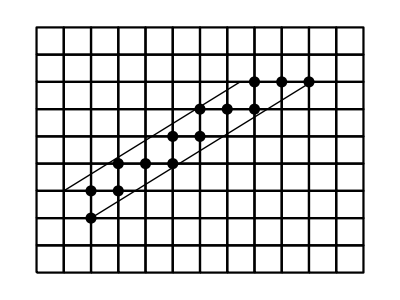

```mathematica
selPts=r/@Range[0,Fibonacci[n+2]];
Graphics[{{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
c=Fibonacci[n+1]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
c=Cos[θ];
s=Fibonacci[n]/√(Fibonacci[n]^2+Fibonacci[n+1]^2);
s=Sin[θ];
(* projection of a selected point on the cut axis *)
proj[{x_,y_}]:={c,s}(x c + y s);
(* projection of a selected point on the window *)
orthProj[r_]:=r-proj[r];
```

```mathematica
(* project selected points into the parallel space *)
projPts=proj/@selPts;
(* project selected points into the perp space *)
orthPts=orthProj/@selPts;
(* lines from pts to parallel proj *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
(* lines from pts to perp proj *)
orthLines=MapThread[Line[{#1,#2}]&,{selPts,orthPts}];
```

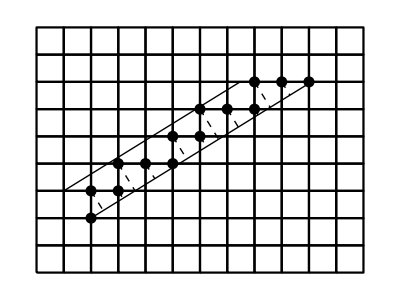

```mathematica
Graphics[{{Dashed,projLines},{PointSize[0.02],Point[selPts]},cut,window,{EdgeForm[{Thickness[0.004],Opacity[1]}],Opacity[0],square/@z2}}]
```

```mathematica
(* on the cut, alternate two types of lines *)
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
col1=comp;
col2=BostonBlue;
(* draw a line bewteen points i and i+1 along the cut *)
(* (rf-ri)[[1]] is either 0 (short) or 1 (long) *)
th=0.004;
(*cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Blend[{col1,col2},(rf-ri)[[1]]],{Thickness[th],Line[{proj[ri],proj[rf]}]}}]*)

(* draw a double line for strong bonds, a single line for weak bonds *) 
(* draw a double line *)
DoubleLine[coords_,spacing_]:=Block[{Δv=coords[[2]]-coords[[1]],norm},
Δv=Δv/Norm[Δv];
(* vector normal to the direction of the line *)
norm={-Δv[[2]],Δv[[1]]};
Line[Map[Function[y,coords+y{norm,norm}],{-spacing/2,spacing/2}]]
]
spac=0.1;
cutLine[i_]:=Block[{ri=r[i],rf=r[i+1]},{Thickness[th],If[(rf-ri)[[1]]==1,Line[{proj[ri],proj[rf]}],DoubleLine[{proj[ri],proj[rf]},spac]]}]

(* color projected point in red for atoms, in blue for molecules *)
coloredPt[i_]:=Block[{ri=r[i-1],rf=r[i+1]},{If[(rf-ri)[[1]]==2,BostonBlue,comp],Point[selPts[[i+1]]]}]

(* rotation matrix *)
rot=RotationMatrix[θ];
(* windows width *)
W=Sin[θ]+Cos[θ];
(* spacing in perp space *)
δW=W/Fibonacci[n+2];
```

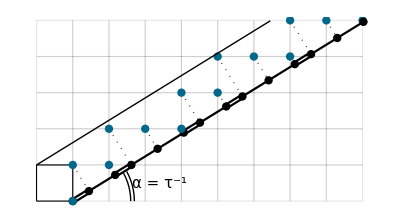

```mathematica
(* same thing, but with focus on parallel space *)
z2p=Flatten[Table[{x,y},{x,-1,Fibonacci[n+1]-1},{y,0,Fibonacci[n]-1}],1];
(* project selected points into the parallel space *)
projPts=proj/@selPts;
(* lines from pts to parallel proj *)
projLines=MapThread[Line[{#1,#2}]&,{selPts,projPts}];
(* projection angle *)
ang={Text[st@"α = τ^-1",{2.4,0.5}],Circle[{0,0},#,{0,0.9 ArcTan[Fibonacci[n]/Fibonacci[n+1]]}]&/@{1.6,1.7}};
(* couplings *)
tts=Text[st@"t_s",{4.55,2.5}];
ttw=Text[st@"t_w",{4.05,2.15}];
thicksquare={EdgeForm[Directive[Opacity[1],Thickness[0.002]]],Opacity[0],square[{-1,0}]};
grid={EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2p};
greyline={Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]};
Graphics[{grid,thicksquare,ang,{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,projLines},{PointSize[0.015],Point[projPts],{BostonBlue,Point[selPts[[#+1]]]}&/@Range[0,Fibonacci[n+2]]},window}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project.pdf",%]
```

/home/nicolas/git/PhD_thesis/img0/cut_and_project.pdf

```mathematica
co[i_]:=Mod[Fibonacci[n+1]i,Fibonacci[n+2]];
```

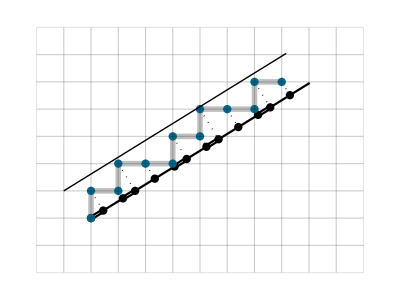

```mathematica
(* atomic surface *)
surf={BostonBlue,Thickness[th],Line[{{0,0},rot.{0,W}}]};
graph=Graphics[{{Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]},{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,projLines},{PointSize[0.015],Point[projPts],{BostonBlue,Point[selPts[[#+1]]]}&/@Range[0,Fibonacci[n+2]-1]},window,{EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2}}}]
```

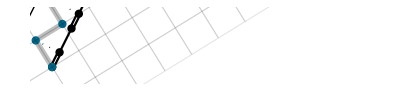

```mathematica
orig={0,0};
δ=0.5;
v=.5;
(* text displacement *)
txtδ=-.15;
(* font size *)
ftsiz=5;
(* conumbering *)
style[string_]:=Style[string,Directive[FontSize->ftsiz,FontFamily->"Linux Libertine"]]
conum=Table[Text[style[i],{txtδ,δW i}],{i,0,Fibonacci[n+2]-1}];
(* numbering in parallel space *)
rotinv=RotationMatrix[θ]; (* rotation from tilted to non tilted *)
pts=Dot[rotinv,#]&/@projPts; (* coords of the points in parallel space, non tilted *)
num=Table[Text[style[co[i]],pts[[i+1]]+{0,txtδ}],{i,0,Fibonacci[n+2]-1}]; 
Graphics[{Rotate[graph,θ,orig]/.Graphics->Identity},PlotRange->{{-δ,√(Fibonacci[n]^2+Fibonacci[n+1]^2)+δ},{-v,W+v}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project_rotated.pdf",%]
```

/home/nicolas/git/PhD_thesis/img0/cut_and_project_rotated.pdf

```mathematica
(* inserting brackets to mark atomic and molecular sites in perp space *)
(* NOTE: the code is extremely ugly: everything is done by hand... *)
curve=First[First[ImportString[ExportString[Style["{",FontFamily->"Linux Libertine",FontSize->12],"PDF"],"TextMode"->"Outlines"]]];
cg=Graphics[curve];
```

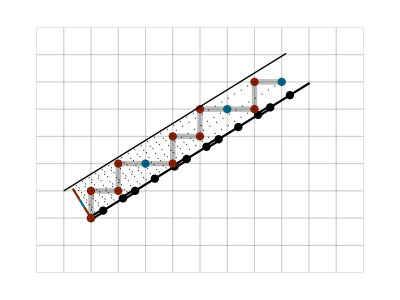

```mathematica
graph=Graphics[{{Directive[Gray,Opacity[0.5],Thickness[0.01]],Line[selPts]},{cutLine/@Range[0,Fibonacci[n+2]-1],{Dotted,orthLines},windMol,windAt,{PointSize[0.015],Point[projPts],coloredPt/@Range[0,Fibonacci[n+2]-1]},window,{EdgeForm[Directive[Opacity[1],Opacity[0.1]]],Opacity[0],square/@z2}}}]
```

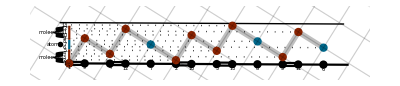

```mathematica
θ=-ArcTan[Fibonacci[n]/Fibonacci[n+1]];
orig={0,0};
δ=0.5;
v=0.5;
(* text displacement *)
txtδ=-.15;
(* font size *)
ftsiz=5;
(* conumbering *)
style[string_]:=Style[string,Directive[FontSize->ftsiz,FontFamily->"Linux Libertine"]]
conum=Table[Text[style[i+1],{txtδ,δW i}],{i,0,Fibonacci[n+2]-1}];
(* numbering in parallel space *)
rotinv=RotationMatrix[θ]; (* rotation from tilted to non tilted *)
pts=Dot[rotinv,#]&/@projPts; (* coords of the points in parallel space, non tilted *)
num=Table[Text[style[co[i]+1],pts[[i+1]]+{0,txtδ}],{i,0,Fibonacci[n+2]-1}]; 
Graphics[{Rotate[graph,θ,orig]/.Graphics->Identity,conum,num,Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,1.05},{0,0},{1,0.5}],Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,0.205},{0,0},{1,0.5}],Inset[Pane[cg,ImageSizeAction->"ResizeToFit"],{2txtδ,0.66},{0,0},{1,0.3}],Text[style["atoms"],{2 txtδ-0.2,W/2-δW/2}],Text[style["molecules"],{2 txtδ-0.3,(Fibonacci[n-1]+1) δW/2}],Text[style["molecules"],{2 txtδ-0.3,Fibonacci[n+1]δW+(Fibonacci[n-1]+1) δW/2}]},PlotRange->{{-2.2δ,√(Fibonacci[n]^2+Fibonacci[n+1]^2)+δ},{-v,W+v}}]
```

```mathematica
Export[NotebookDirectory[]<>"cut_and_project_perp_projections.pdf",%]
```

/home/nicolas/git/PhD_thesis/img0/cut_and_project_perp_projections.pdf